```mathematica
FourierTransform[Sin[Subscript[Ω, drive] * t],t,ω]
```

ⅈ √(π/2) DiracDelta[ω-Ω_drive]-ⅈ √(π/2) DiracDelta[ω+Ω_drive]

```mathematica
ftilde= FullSimplify[FourierTransform[Sin[Subscript[Ω, drive]*t]*(1 + A*HeavisideTheta[t]),t,ω]]
```

ⅈ √(π/2) DiracDelta[ω-Ω_drive]+1/2 ⅈ A √(π/2) DiracDelta[ω-Ω_drive]-ⅈ √(π/2) DiracDelta[ω+Ω_drive]-1/2 ⅈ A √(π/2) DiracDelta[ω+Ω_drive]+(A Ω_drive)/(√(2 π) (-ω^2+Ω_drive^2))

Now bandpass (cut off frequencies above Ω_drive/2 and IFT back):

```mathematica
ffilt = InverseFourierTransform[ftilde * HeavisideTheta[Subscript[Ω, drive]/2 - ω],ω,t]
```

1/(8 π t)ⅇ^(-ⅈ t Ω_drive) (-ⅈ A (-1+ⅇ^(2 ⅈ t Ω_drive)) π Abs[t]+2 t (A ⅇ^(2 ⅈ t Ω_drive) CosIntegral[-(3 t Ω_drive)/2]-A CosIntegral[(t Ω_drive)/2]+A Log[t]-A ⅇ^(2 ⅈ t Ω_drive) Log[t]-A Log[Abs[t]]+A ⅇ^(2 ⅈ t Ω_drive) Log[Abs[t]]-ⅈ A SinIntegral[(t Ω_drive)/2]-ⅈ A ⅇ^(2 ⅈ t Ω_drive) SinIntegral[(3 t Ω_drive)/2]+2 ⅈ π UnitStep[-Ω_drive]+ⅈ A π UnitStep[-Ω_drive]-2 ⅈ ⅇ^(2 ⅈ t Ω_drive) π UnitStep[Ω_drive]-ⅈ A ⅇ^(2 ⅈ t Ω_drive) π UnitStep[Ω_drive]))

Now integrate up to the resonator bandwidth, Ω_0< Ω_drive:

```mathematica
impulse = Integrate[ffilt, {t,0,Subscript[Ω, 0]}, Assumptions->{Subscript[Ω, 0]>0&&Subscript[Ω, drive]>0, Subscript[Ω, 0]< Subscript[Ω, drive]}]
```

-1/(8 π Ω_drive)ⅇ^(-ⅈ Ω_0 Ω_drive) (A π-4 ⅇ^(ⅈ Ω_0 Ω_drive) π-3 A ⅇ^(ⅈ Ω_0 Ω_drive) π+4 ⅇ^(2 ⅈ Ω_0 Ω_drive) π+3 A ⅇ^(2 ⅈ Ω_0 Ω_drive) π-ⅈ A ⅇ^(ⅈ Ω_0 Ω_drive) CosIntegral[-3/2 Ω_0 Ω_drive]+2 ⅈ A ⅇ^(2 ⅈ Ω_0 Ω_drive) CosIntegral[-3/2 Ω_0 Ω_drive]-ⅈ A ⅇ^(ⅈ Ω_0 Ω_drive) CosIntegral[-1/2 Ω_0 Ω_drive]+2 ⅈ A CosIntegral[(Ω_0 Ω_drive)/2]-3 ⅈ A ⅇ^(ⅈ Ω_0 Ω_drive) ExpIntegralEi[-1/2 ⅈ Ω_0 Ω_drive]+ⅈ A ⅇ^(ⅈ Ω_0 Ω_drive) ExpIntegralEi[-3/2 ⅈ Ω_0 Ω_drive]-ⅈ A ⅇ^(ⅈ Ω_0 Ω_drive) Log[9/5]-ⅈ A ⅇ^(ⅈ Ω_0 Ω_drive) Log[5]-2 A SinIntegral[(Ω_0 Ω_drive)/2]-A ⅇ^(ⅈ Ω_0 Ω_drive) SinIntegral[(Ω_0 Ω_drive)/2]-A ⅇ^(ⅈ Ω_0 Ω_drive) SinIntegral[(3 Ω_0 Ω_drive)/2]+2 A ⅇ^(2 ⅈ Ω_0 Ω_drive) SinIntegral[(3 Ω_0 Ω_drive)/2])

```mathematica
impulse/.{Subscript[Ω, drive]->1, A->1}
```

-1/(8 π)ⅇ^(-ⅈ Ω_0) (π-7 ⅇ^(ⅈ Ω_0) π+7 ⅇ^(2 ⅈ Ω_0) π-ⅈ ⅇ^(ⅈ Ω_0) CosIntegral[-(3 Ω_0)/2]+2 ⅈ ⅇ^(2 ⅈ Ω_0) CosIntegral[-(3 Ω_0)/2]-ⅈ ⅇ^(ⅈ Ω_0) CosIntegral[-Ω_0/2]+2 ⅈ CosIntegral[Ω_0/2]-3 ⅈ ⅇ^(ⅈ Ω_0) ExpIntegralEi[-(ⅈ Ω_0)/2]+ⅈ ⅇ^(ⅈ Ω_0) ExpIntegralEi[-(3 ⅈ Ω_0)/2]-ⅈ ⅇ^(ⅈ Ω_0) Log[9/5]-ⅈ ⅇ^(ⅈ Ω_0) Log[5]-2 SinIntegral[Ω_0/2]-ⅇ^(ⅈ Ω_0) SinIntegral[Ω_0/2]-ⅇ^(ⅈ Ω_0) SinIntegral[(3 Ω_0)/2]+2 ⅇ^(2 ⅈ Ω_0) SinIntegral[(3 Ω_0)/2])

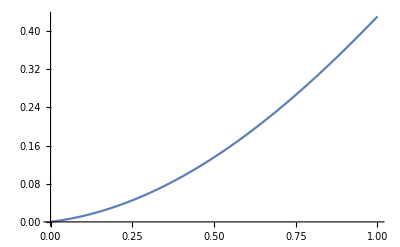

```mathematica
Plot[Re[impulse/.{Subscript[Ω, drive]->1, A->1}], {Subscript[Ω, 0], 0 , 1}]
```

```mathematica
ftilde= FourierTransform[Sin[Subscript[Ω, drive]*t]*(1 + A*HeavisideTheta[t]),t,ω]
```

ⅈ √(π/2) DiracDelta[ω-Ω_drive]+1/2 ⅈ A √(π/2) DiracDelta[ω-Ω_drive]-ⅈ √(π/2) DiracDelta[ω+Ω_drive]-1/2 ⅈ A √(π/2) DiracDelta[ω+Ω_drive]+(A Ω_drive)/(√(2 π) (-ω^2+Ω_drive^2))

```mathematica
x = InverseFourierTransform[ftilde/(Subscript[Ω, 0]^2-ω^2+ⅈ*γ*ω), ω, t, Assumptions->{A>0, Subscript[Ω, drive]>0, γ>0, Subscript[Ω, 0]>0}]
```

InverseFourierTransform[1/(ⅈ γ ω-ω^2+Ω_0^2)(ⅈ √(π/2) DiracDelta[ω-Ω_drive]+1/2 ⅈ A √(π/2) DiracDelta[ω-Ω_drive]-ⅈ √(π/2) DiracDelta[ω+Ω_drive]-1/2 ⅈ A √(π/2) DiracDelta[ω+Ω_drive]+(A Ω_drive)/(√(2 π) (-ω^2+Ω_drive^2))),ω,t,Assumptions→{A>0,Ω_drive>0,γ>0,Ω_0>0}]

```mathematica
FullSimplify[x]
```

-(ⅈ ((2+A+A Sign[t]) Sin[t Ω_drive]+(A ⅇ^(-Abs[t] √(-ⅈ γ-Ω_0^2)) Ω_drive)/(√(-ⅈ γ-Ω_0^2))))/(2 (γ-ⅈ Ω_0^2+ⅈ Ω_drive^2))

```mathematica
x/.{A->1, Subscript[Ω, drive]->1,Subscript[Ω, 0]->0.1,γ->0.01}
```

(-3 ⅈ ⅇ^(-ⅈ t) (-1+ⅇ^(2 ⅈ t))+2 ⅇ^(-Abs[t]/(√(-1/(0.01+ⅈγω)))) √(-1/(0.01+ⅈγω))-ⅈ ⅇ^(-ⅈ t) (-1+ⅇ^(2 ⅈ t)) Sign[t])/(4 (-0.99+ⅈγω))

```mathematica
FullSimplify[Re[x]]
```

1/4 Re[(2 (2+A+A Sign[t]) Sin[t Ω_drive]+2 A ⅇ^(-Abs[t]/(√(-1/(ⅈγω+Ω_0^2)))) √(-1/(ⅈγω+Ω_0^2)) Ω_drive)/(ⅈγω+Ω_0^2-Ω_drive^2)]

```mathematica
FullSimplify[x, Assumptions->{Subscript[Ω, drive]>0, Subscript[Ω, 0]>0, γ>0, A>0}]
```

1/(4 (-ⅈ γ Ω_0-Ω_0^2+Ω_drive^2))ⅈ ⅇ^(-ⅈ t Ω_drive) ((-1+ⅇ^(2 ⅈ t Ω_drive)) (2+A+A Sign[t])+2 ⅈ A ⅇ^(ⅈ (Abs[t] √(Ω_0 (ⅈ γ+Ω_0))+t Ω_drive)) √(-1/(Ω_0 (ⅈ γ+Ω_0))) Ω_drive)

```mathematica
FullSimplify[Im[x], Assumptions->{Subscript[Ω, drive]>0, Subscript[Ω, 0]>0, γ>0, A>0, B>0}]
```

1/4 Re[1/(-ⅈ γ Ω_0-Ω_0^2+Ω_drive^2)ⅇ^(-ⅈ t Ω_drive) ((-1+ⅇ^(2 ⅈ t Ω_drive)) (2 A+B+B Sign[t])+2 ⅈ B ⅇ^(ⅈ (Abs[t] √(Ω_0 (ⅈ γ+Ω_0))+t Ω_drive)) √(-1/(Ω_0 (ⅈ γ+Ω_0))) Ω_drive)]

```mathematica
x = InverseFourierTransform[1/(Subscript[Ω, 0]^2 - ω^2 + ⅈ*γ*Subscript[Ω, 0]), ω, t, Assumptions->{Subscript[Ω, 0]>0,γ>0}]
```

-(ⅇ^(-Abs[t] √((-ⅈ γ-Ω_0) Ω_0)) √(π/2))/(√(-1-(ⅈ γ)/Ω_0) Ω_0)

```mathematica
FullSimplify[x]
```

-(ⅇ^(-Abs[t] √((-ⅈ γ-Ω_0) Ω_0)) √(π/2))/(√(-1-(ⅈ γ)/Ω_0) Ω_0)